# Leakage Analysis of pipe bombs

```mathematica
dataRoot=NotebookDirectory[]
```

F:\Data\general\

## RG59 stripped

```mathematica
fileList="LeakageCurrent19Jun130"<>ToString[#]<>".csv"&/@Range[1,2]
```

{LeakageCurrent19Jun1301.csv,LeakageCurrent19Jun1302.csv}

```mathematica
datIncHeads=Import[dataRoot<>#,"CSV"]&/@fileList;
```

```mathematica
dat=Drop[#,8]&/@datIncHeads;
```

```mathematica
getNorthDat[list2d_]:=First[#]&/@list2d
getSouthDat[list2d_]:=Last[#]&/@list2d
```

```mathematica
switchLength=20;
tolerance=20;
```

```mathematica
dataS=getSouthDat/@dat;
```

```mathematica
dataN=getNorthDat/@dat;
```

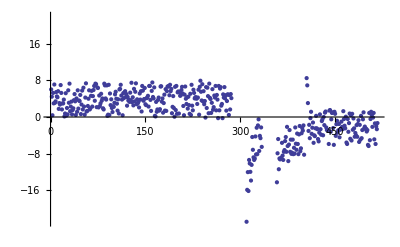
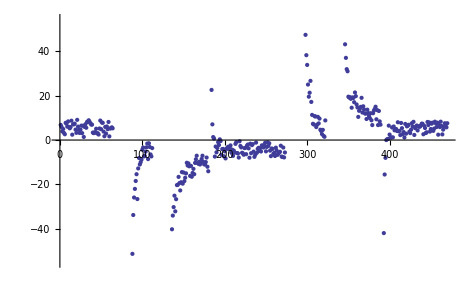

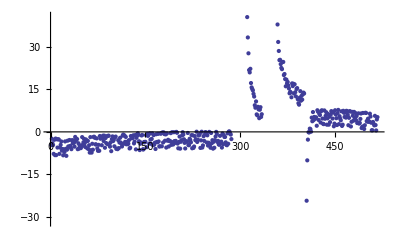
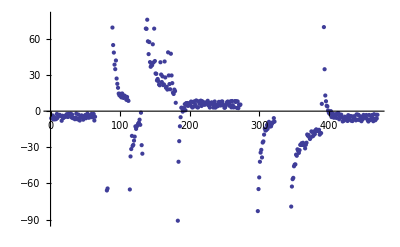

```mathematica
ListPlot/@dataS
ListPlot/@dataN
```

```mathematica
MinPosition=Position [data,Min[dat]]⟦1⟧⟦1⟧
```

206

```mathematica
lastSwitch=Take[data,{MinPosition,Length[data]}];
```

```mathematica
lastSwitch;
```

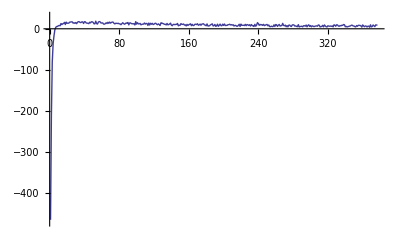

```mathematica
ListPlot[lastSwitch,Joined->True,PlotRange->{All,{-470,30}}]
```

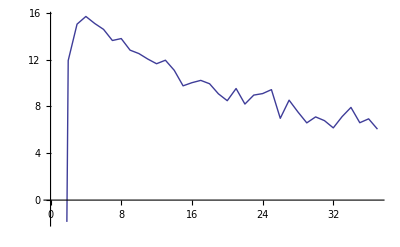

```mathematica
ListPlot[Mean/@Partition[lastSwitch,10],Joined->True]
```

```mathematica
datToFit=Drop[lastSwitch,100];
```

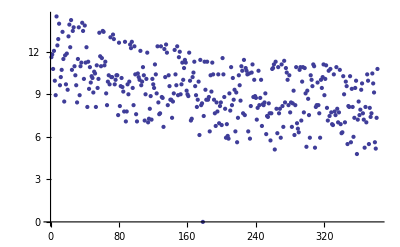

```mathematica
ListPlot[datToFit]
```

```mathematica
fit=NonlinearModelFit[datToFit,A  ⅇ^(-t/τ),{{A,20},{τ,70}},t]
```

FittedModel[11.1942 ⅇ^(-0.000974663 t)]

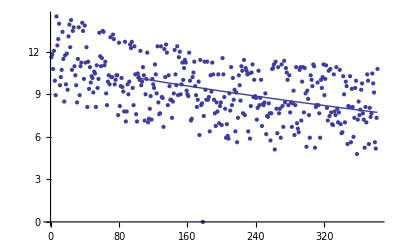

```mathematica
Show[ListPlot[datToFit],Plot[fit[x],{x,100,Length[datToFit]}]]
```

```mathematica
τ/.fit["BestFitParameters"]
```

1541.56

```mathematica
fit["ParameterErrors"]
```

{0.145142,434.027}

```mathematica
datToFit=Drop[getSouthDat[dat],10];
```

```mathematica
fit=NonlinearModelFit[datToFit,A  ( ⅇ^(-t/τ))+B,{{A,-5},{τ,200},{B,-11}},t]
```

FittedModel[-11.0855-3.41862 ⅇ^(-0.00285045 t)]

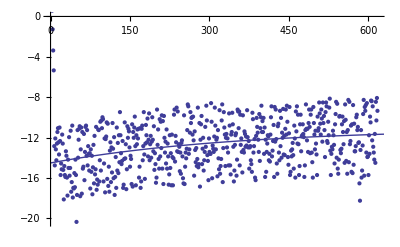

```mathematica
Show[ListPlot[getSouthDat[dat]],Plot[fit[x],{x,0,1000}]]
```

```mathematica
τ/.fit["BestFitParameters"]
```

350.821

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
trimSwitches[dat_]:=Module[{firstTooBigVal,firstTooBigPlace,newDat,m},
If[Length[Select[dat,Abs[#]>tolerance&,1]]==0,
dat,
firstTooBigVal=Select[dat,Abs[#]>tolerance&,1]⟦1⟧;
firstTooBigPlace=First[Position[dat,firstTooBigVal]]⟦1⟧;
m=firstTooBigPlace+switchLength;
If[m>Length[dat],
newDat=Drop[dat,{firstTooBigPlace,Length[dat]}],
newDat=Drop[dat,{firstTooBigPlace,firstTooBigPlace+switchLength}]
];
trimSwitches[newDat]
]
]
```

```mathematica
centreData[dat_]:=dat-TrimmedMean[dat]
```

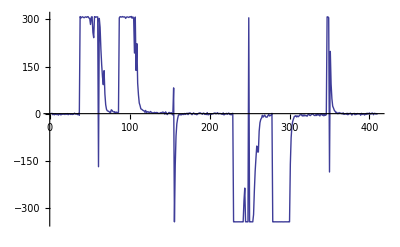

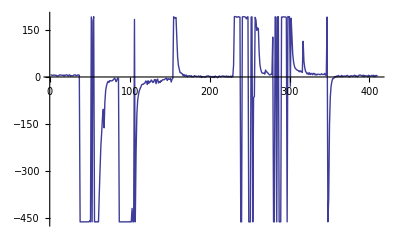

```mathematica
ListPlot[{getSouthDat[dat]},PlotRange->{All,All},Joined->True]
ListPlot[{getNorthDat[dat]},PlotRange->{All,All},Joined->True]
```

```mathematica
trimmedNorthData=centreData[trimSwitches[getNorthDat[dat]]];
trimmedSouthData=centreData[trimSwitches[getSouthDat[dat]]];
```

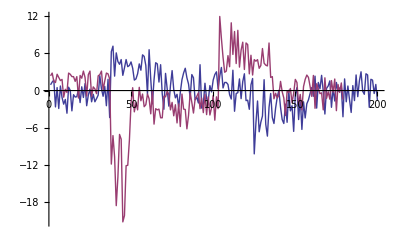

```mathematica
ListPlot[{trimmedSouthData,trimmedNorthData},PlotRange->{All,All},Joined->True]
```

```mathematica
dischargeTol=6.5;
```

```mathematica
dischargeVals[dat_]:=Select[dat,Abs[#]>dischargeTol&]
dischargeCounts[dat_]:=Length[dischargeVals[dat]]
```

```mathematica
polPeriod = 100(*ms*);
timeInterval = 5*60*1000(*ms*);
```

```mathematica
interval= timeInterval/polPeriod;
```

```mathematica
binnedTrimmedNorthData=Partition[trimmedNorthData,interval];
binnedTrimmedSouthData=Partition[trimmedSouthData,interval];
```

```mathematica
northCounts=dischargeCounts[#]&/@binnedTrimmedNorthData
southCounts=dischargeCounts[#]&/@binnedTrimmedSouthData
```

{65,30,18,28,46,27,21,16,44,16,24,112,35,34,42,22,33,32,67,83}

{418,295,197,81,60,58,34,18,17,15,9,16,10,7,4,25,47,38,99,101}

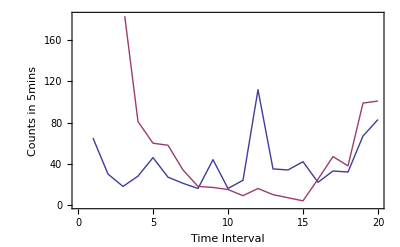

```mathematica
ListPlot[{northCounts,southCounts},Axes->False,Frame->True,FrameLabel->{"Time Interval","Counts in 5mins"},Joined->True]
```